```mathematica
h[x_]:=Piecewise[{{1+Subscript[c, 0,1] x+Subscript[c, 0,2] x^2+Subscript[c, 0,3] x^3+Subscript[c, 0,4] x^4, 0≤x≤1/2}, {Subscript[c, 1,1](x-1)+Subscript[c, 1,2](x-1)^2+Subscript[c, 1,3](x-1)^3+Subscript[c, 1,4](x-1)^4, 1/2<x≤3/2}, {Subscript[c, 2,1](x-2)+Subscript[c, 2,2](x-2)^2+Subscript[c, 2,3](x-2)^3+Subscript[c, 2,4](x-2)^4, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
AllVars={Subscript[c, 0,1],Subscript[c, 0,2],Subscript[c, 0,3],Subscript[c, 0,4],Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3],Subscript[c, 1,4],Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3],Subscript[c, 2,4]};
```

```mathematica
(*Continuity*)
C1=Limit[h[x],x->1/2,Direction->1]==Limit[h[x],x->1/2,Direction->-1]
C2=Limit[h[x],x->3/2,Direction->1]==Limit[h[x],x->3/2,Direction->-1]
C3=Limit[h[x],x->5/2,Direction->1]==Limit[h[x],x->5/2,Direction->-1]
```

1/16 (16+8 c_(0,1)+4 c_(0,2)+2 c_(0,3)+c_(0,4))==1/16 (-8 c_(1,1)+4 c_(1,2)-2 c_(1,3)+c_(1,4))

1/16 (8 c_(1,1)+4 c_(1,2)+2 c_(1,3)+c_(1,4))==1/16 (-8 c_(2,1)+4 c_(2,2)-2 c_(2,3)+c_(2,4))

1/16 (8 c_(2,1)+4 c_(2,2)+2 c_(2,3)+c_(2,4))==0

```mathematica
(*Partition of unity and linear term*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c_(0,1),c_(0,2)+2 (c_(1,2)+c_(2,2)),c_(0,3),c_(0,4)+2 (c_(1,4)+c_(2,4))}

{0,-2 c_(1,1)-4 c_(2,1),0,-2 (c_(1,3)+2 c_(2,3))}

```mathematica
GenSols=Solve[{
	C1,C2,C3,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T0[[5]]==0,
	T1[[2]]==1,
	T1[[4]]==0
	},
	AllVars
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c_(0,1)→0,c_(0,3)→0,c_(1,3)→-6-2 c_(0,2)-(c_(0,4))/2-4 c_(1,1),c_(1,4)→4-4 c_(1,2),c_(2,1)→-1/4-(c_(1,1))/2,c_(2,2)→-(c_(0,2))/2-c_(1,2),c_(2,3)→3+c_(0,2)+(c_(0,4))/4+2 c_(1,1),c_(2,4)→-4-(c_(0,4))/2+4 c_(1,2)}}

```mathematica
RegionXY[k_]:={Quotient[k,2],1+Quotient[-k,2]};
Regions=Table[RegionXY[k],{k,-4,7}]-1/2
```

{{-5/2,5/2},{-5/2,3/2},{-3/2,3/2},{-3/2,1/2},{-1/2,1/2},{-1/2,-1/2},{1/2,-1/2},{1/2,-3/2},{3/2,-3/2},{3/2,-5/2},{5/2,-5/2},{5/2,-7/2}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
φ=1/2;
W[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF=∑_(i=-5)^6 ∑_(j=-5)^6 W[i-j]f[x-i,y-j]/.GenSol;
SimplifySquare[f_,x0_,y0_]:=Simplify[f,x>x0&&x<x0+1&&y>y0&&y<y0+1];
DSimplifySquare[f_,{x0_,y0_}]:=Simplify[D[SimplifySquare[f,x0,y0],{{x,y}}]];
DSumF=ParallelMap[DSimplifySquare[SumF,#]&,Regions];
```

```mathematica
AnisoInt[df_,{x0_,y0_}]:=Simplify[Integrate[Expand[(df.{1,1})^2],{x,x0,x0+1},{y,y0,y0+1}]];
AnisoInts=Parallelize[MapThread[AnisoInt,{DSumF,Regions}]];
Err=Simplify[Total[AnisoInts]]
```

1/69363302400(3435022080 c_(0,2)^4+13203915 c_(0,4)^4+48 c_(0,4)^3 (13451975+150478 c_(1,1)+2795 c_(1,2))+10752 c_(0,2)^3 (3711112+316425 c_(0,4)-6012 c_(1,1)+13794 c_(1,2))+64 c_(0,4)^2 (222183873+1739784 c_(1,1)^2-39564 c_(1,2)+37016 c_(1,2)^2-6 c_(1,1) (100757+23092 c_(1,2)))+2048 c_(0,4) (58355292+126756 c_(1,1)^3-5002167 c_(1,2)-286130 c_(1,2)^2-4930 c_(1,2)^3-6 c_(1,1)^2 (-331526+21335 c_(1,2))+c_(1,1) (5645217+223554 c_(1,2)-46248 c_(1,2)^2))+8192 (46358295+528444 c_(1,1)^3+507024 c_(1,1)^4-8451174 c_(1,2)+1896418 c_(1,2)^2+111088 c_(1,2)^3+14080 c_(1,2)^4-36 c_(1,1) (-531177-17935 c_(1,2)+4449 c_(1,2)^2)+6 c_(1,1)^2 (1429427+36248 c_(1,2)+12032 c_(1,2)^2))+32 c_(0,2)^2 (39789115 c_(0,4)^2+8 c_(0,4) (118209037+654822 c_(1,1)+85559 c_(1,2))+32 (191723345+887544 c_(1,1)^2-634372 c_(1,2)+202904 c_(1,2)^2-630 c_(1,1) (-2063+1004 c_(1,2))))+64 c_(0,2) (3306360 c_(0,4)^3+c_(0,4)^2 (120471210+1169382 c_(1,1)+98707 c_(1,2))+8 c_(0,4) (203126499+1056384 c_(1,1)^2+c_(1,1) (879834-385536 c_(1,2))-1770536 c_(1,2)-15208 c_(1,2)^2)+128 (52225182+126756 c_(1,1)^3-2843219 c_(1,2)+175864 c_(1,2)^2+20590 c_(1,2)^3-126 c_(1,1)^2 (-20259+251 c_(1,2))-3 c_(1,1) (-2311657+5498 c_(1,2)+15416 c_(1,2)^2))))

```mathematica
FreeVars=Variables[Err];
DErr=Simplify[D[Err,{FreeVars}]];
H=D[DErr,{FreeVars}];
Sols=Solve[DErr==0,FreeVars,Reals];
TableForm[{Range[Length[Sols]],Err/.N[Sols,32],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1 | 0.06881454653131627777477218405 | True

{c_(0,1)→0,c_(0,3)→0,c_(1,3)→0.51980718987666977283111451604,c_(1,4)→-2.685053062105869853950586210222,c_(2,1)→0.1633471674323476051066064449425,c_(2,2)→-0.4609134696644818993482442379065,c_(2,3)→-0.25990359493833488641555725802,c_(2,4)→1.056683729075816529371239908126,c_(0,2)→-2.4206995917239711282788046292981,c_(0,4)→3.2567386660601066491586926041917,c_(1,1)→-0.826694334864695210213212889885,c_(1,2)→1.6712632655264674634876465525555}

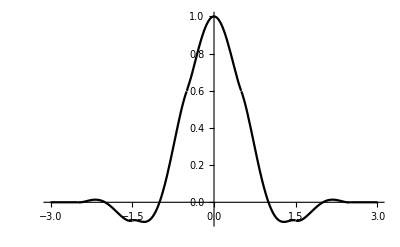

```mathematica
NSol=N[Sols[[1]],32];
FullSol=Join[GenSol/.NSol,NSol]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```